```mathematica
ClearAll["Global`*"];
(* Image Source: http://beforeitsnews.com/alternative/2015/01/colossal-rogue-star-on-collision-course-with-our-solar-systemin-240000-years-3087922.html *)
Solar = Import["C:\\Users\\lingbotang\\Downloads\\Samples\\Solar.jpg"];
(* Image Source: https://www.chemcomp.com/journal/molorbs.htm *)
Atomic = Import["C:\\Users\\lingbotang\\Downloads\\Samples\\Atomic.gif"];
(* Image Source: https://www.e-education.psu.edu/astro801/content/l3_p6.html *)
Elevel = Import["C:\\Users\\lingbotang\\Downloads\\Samples\\EnergyLevel.jpg"];
```

```mathematica
(* Sample *)
DynamicModule[{pt={0,0},c="Red"},ClickPane[Framed@Graphics[{Red,Disk[],Black,Dynamic@Arrow[{{-2,0},pt}],Dynamic@Text[Dynamic[c],{-2,0}]}],(pt=#;
c=If[Norm[pt]<1,"Red","White"])&]];
```

```mathematica
(*clip white borders*)img=ImageCrop[Import["http://i.stack.imgur.com/La8Zs.jpg"]];

Plot[-14/81 x (x-18),{x,-2,19},PlotRange->{-2,16},PlotStyle->Directive[Red,Thick,Dashed],Prolog->{Texture[img],Polygon[{Scaled[{0,0}],Scaled[{1,0}],Scaled[{1,1}],Scaled[{0,1}]},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Ticks->None]
```

-Graphics-

```mathematica
ControllerManipulate[Plot[{Sin[x+a]+b,Sinc[x+c]+d},{x,-2 Pi,2 Pi},PlotRange->2],{a,0,10},{b,0,1},{c,0,10},{d,0,1}]
```

```mathematica
(* Working *) 
DynamicModule[{lectureText={"Solar System Simulation\nThis is an old simulation that has long been abandoned.\nBut it's still meaniful to show the history","Accurate Model\nThis is an relatively accurate model to describe the motion of electrons\nElectrons are magic, they jump from different energy levels.\nSo it looks like a cloud","Energy Levels\nElectrons jump to a lower energy level when they emit the energy,\nwhile they jump to higher energy level when they absorb the energy from external source (like light)"},clicked=1},EventHandler[Grid[{{Row[{Annotation[Image[Solar,ImageSize->Small],1,"Mouse"],Annotation[Image[Atomic,ImageSize->Small],2,"Mouse"],Annotation[Image[Elevel,ImageSize->Small],3,"Mouse"]}]},{Dynamic@Text[lectureText[[clicked]]]}}],{"MouseClicked":>(clicked = MouseAnnotation[])}]]
```

```mathematica
(* Graphics *)
```

```mathematica
DynamicModule[{lectureGraphics = {MouseAppearance[SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Blue,Mesh-> None,Boxed-> False,Axes->False],"DragGraphics"],MouseAppearance[SphericalPlot3D[Evaluate@Abs@SphericalHarmonicY[3,1,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotStyle->Red,Mesh->None,Boxed-> False,Axes->False],"DragGraphics"],MouseAppearance[ParametricPlot3D[{Cos[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u/2] Sin[v]+Cos[u/2] Sin[2 v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->FaceForm[Green,Green],Mesh->None,Boxed->False,Axes->False],"DragGraphics"],MouseAppearance[RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Orange,Mesh->None,Boxed->False,Axes->False],"DragGraphics"]},clicker = 1},
EventHandler[Grid[{{Row[{Annotation[MouseAppearance[Graphics3D[{Blue,Sphere[{Cos[0],Sin[0],0},0.2]},Boxed->False],"LinkHand"],1,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Red,Sphere[{Cos[0],Sin[0],0},0.2]},Boxed->False],"LinkHand"],2,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Green,Sphere[{Cos[0],Sin[0],0},0.2]},Boxed->False],"LinkHand"],3,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Orange,Sphere[{Cos[0],Sin[0],0},0.2]},Boxed->False],"LinkHand"],4,"Mouse"]}]},{Dynamic@Text[lectureGraphics[[clicker]]]}}],{"MouseClicked":>(clicker = MouseAnnotation[])}]]
```

```mathematica
DynamicModule[{lectureGraphics = {MouseAppearance[SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Blue,Mesh-> None,Boxed-> False,Axes->False],"DragGraphics"],MouseAppearance[SphericalPlot3D[Evaluate@Abs@SphericalHarmonicY[3,1,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotStyle->Red,Mesh->None,Boxed-> False,Axes->False],"DragGraphics"],MouseAppearance[ParametricPlot3D[{Cos[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u/2] Sin[v]+Cos[u/2] Sin[2 v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->FaceForm[Green,Green],Mesh->None,Boxed->False,Axes->False],"DragGraphics"],MouseAppearance[RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Orange,Mesh->None,Boxed->False,Axes->False],"DragGraphics"]},clicker = 1},
EventHandler[Grid[{{Panel[Annotation[MouseAppearance[Graphics3D[{Blue,Sphere[{0.5*Cos[0],0.5*Sin[0],0},0.2]},Boxed->False],"LinkHand"],1,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Green,Sphere[{1*Cos[0],1*Sin[0],0},0.2]},Boxed->False],"LinkHand"],2,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Red,Sphere[{1.5*Cos[0],1.5*Sin[0],0},0.2]},Boxed->False],"LinkHand"],3,"Mouse"],Annotation[MouseAppearance[Graphics3D[{Orange,Sphere[{2*Cos[0],2*Sin[0],0},0.2]},Boxed->False],"LinkHand"],4,"Mouse"]]},{Dynamic@lectureGraphics[[clicker]]}}],{"MouseClicked":>(clicker = MouseAnnotation[])}]]
```

```mathematica
DynamicModule[{pt={0,0},c="Red"},ClickPane[Framed@Graphics[{Red,Disk[],Black,Dynamic@Arrow[{{-2,0},pt}],Dynamic@Text[Dynamic[c],{-2,0}]}],(pt=#;
c=If[Norm[pt]<1,"Red","White"])&]]
```

```mathematica
DynamicModule[{pt={0,0,0},lectureGraphics = {MouseAppearance[SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Blue,Mesh-> None,Boxed-> False,Axes->False],"DragGraphics"],MouseAppearance[SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Red,Mesh-> None,Boxed-> False,Axes->False],"DragGraphics"]},clicker = 1},ClickPane[Panel[Grid[{{MouseAppearance[Graphics3D[{Blue,Sphere[{0.5*Cos[0],0.5*Sin[0],0},0.2]},Boxed->False],"LinkHand"]},{Dynamic@lectureGraphics[[clicker]]}}]],(pt = #;clicker = If[Norm[pt]<1,1,2]) &]]
```

```mathematica
Manipulate[Graphics[{Circle[{0,0},1],Disk[{0,0},1],Text[Style[Column[{"displacement: ",NumberForm[ω*t,{5,3}]"units","","angular velocity ω: ",NumberForm[ω/(2π),{5,3}]"rev/s",NumberForm[60ω/(2π),{5,3}]"rpm"},Alignment-> Center],14],{2,0}]},PlotRange->All,ImageSize->500],{{t,0,"time"},0,10,ControType-> Trigger},{{ω,3.,"angular velocity"},0.1,5,Appearance-> Labeled}]
```

```mathematica
(* http://demonstrations.wolfram.com/ClickACountry/ *)
Manipulate[
With[{cd=CountryData[]},
With[{ou={CountryData[#,"Name"],CountryData[#,{"SchematicPolygon","Robinson"}]}&/@cd},
Column[{
Graphics[{EdgeForm[Red],Map[If[FreeQ[u,#[[1]]],
Button[{FaceForm[LightGray],#[[2]]},AppendTo[u,#[[1]]]],Button[{FaceForm[Darker[Gray]],#[[2]]},u=DeleteCases[u,#[[1]]]]]&,ou]},Background->Lighter[Blue],ImageSize->600],
Row[{Button[Length[#],u={}],Pane[Text@Row[#,",  "],{400,100},Alignment->{Center,Center}]}]&[Union@u]}]]],
{{u,{}},ControlType->None}]
```

```mathematica
accurateModel = {SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Blue,Mesh-> None,Boxed-> False,Axes->False],
SphericalPlot3D[Evaluate@Abs@SphericalHarmonicY[3,1,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotStyle->Red,Mesh->None,Boxed-> False,Axes->False],
ParametricPlot3D[{Cos[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u/2] Sin[v]+Cos[u/2] Sin[2 v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->FaceForm[Green,Green],Mesh->None,Boxed->False,Axes->False],RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Orange,Mesh->None,Boxed->False,Axes->False]};
Manipulate[
With[{Solar={Graphics3D[{Blue,Sphere[{0.5*Cos[0],0.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Green,Sphere[{1*Cos[0],1*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Red,Sphere[{1.5*Cos[0],1.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Orange,Sphere[{2*Cos[0],2*Sin[0],0},0.2]},Boxed->False]}},
With[{accurate = {accurateModel[[Flatten[Position[Solar,#]]]]} &/@ Solar},
Column[{Show[Solar],accurateModel[#]} &/@accurateModel]]],ControlType-> None,SaveDefinitions->True]
```

```mathematica
Position[<|"a"->1,"b"->2,"c"->3,"d"->4|>,_Integer?PrimeQ]
```

{{Key[b]},{Key[c]}}

```mathematica
Position[<|{1->1+x^2,2-><|"a"->x^2|>,3->x^4,4->a+(1+x^2)^2}|>,x^_]
```

{{Key[1],2},{Key[2],Key[a]},{Key[3]},{Key[4],2,1,2}}

```mathematica
f[x_]:=With[{y=x+1},1+y+y^2]
```

```mathematica
f[a]
```

2+a+(1+a)^2

```mathematica
With[{v={a,b,c},w={x,y,z}},Thread[Unevaluated[Dot[v,w]]]]
```

{a.x,b.y,c.z}

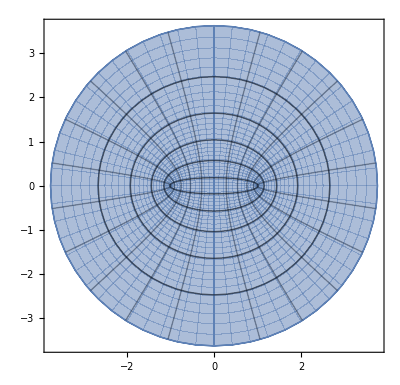

```mathematica
Block[{f=Sin[x+I y]},ParametricPlot[Evaluate[{Re[f],Im[f]}],{x,-Pi,Pi},{y,-2,2},Mesh->10]]
```

```mathematica
Function[u,3+u][x]
```

3+x

```mathematica
(3+#) &
```

3+#1&

```mathematica
(3+#)&[x]
```

3+x

```mathematica
cplus = Plus @@#&
```

Plus@@#1&

```mathematica
cplus[{a,b,c}]
```

a+b+c

```mathematica
Position[accurateModel,#]&/@accurateModel
```

{{{1}},{{2}},{{3}},{{4}}}

```mathematica
Position[accurateModel,#]&@@ accurateModel
```

{{1}}

```mathematica
Solar={Graphics3D[{Blue,Sphere[{0.5*Cos[0],0.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Green,Sphere[{1*Cos[0],1*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Red,Sphere[{1.5*Cos[0],1.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Orange,Sphere[{2*Cos[0],2*Sin[0],0},0.2]},Boxed->False]};
out = accurateModel[[Flatten[Position[Solar,#]]]] &/@ Solar
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}

```mathematica
out[1]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}[1]

```mathematica
out[[1]]
```

{-Graphics3D-}

```mathematica
Flatten[out[1]]
```

{{-Graphics3D-},{-Graphics3D-},{-Graphics3D-},{-Graphics3D-}}[1]

```mathematica
Flatten[out[[1]]]
```

{-Graphics3D-}

```mathematica
accurateModel = {SphericalPlot3D[1+2Cos[2θ],{θ,0,π},{ϕ,0,2π},PlotStyle->Blue,Mesh-> None,Boxed-> False,Axes->False],
SphericalPlot3D[Evaluate@Abs@SphericalHarmonicY[3,1,θ,ϕ],{θ,0,π},{ϕ,0,2π},PlotStyle->Red,Mesh->None,Boxed-> False,Axes->False],
ParametricPlot3D[{Cos[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u] (3+Cos[u/2] Sin[v]-Sin[u/2] Sin[2 v]),Sin[u/2] Sin[v]+Cos[u/2] Sin[2 v]},{u,0,2 Pi},{v,0,2 Pi},PlotStyle->FaceForm[Green,Green],Mesh->None,Boxed->False,Axes->False],RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,0,2 Pi},PlotStyle->Orange,Mesh->None,Boxed->False,Axes->False]};
Manipulate[
With[{Solar={Graphics3D[{Blue,Sphere[{0.5*Cos[0],0.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Green,Sphere[{1*Cos[0],1*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Red,Sphere[{1.5*Cos[0],1.5*Sin[0],0},0.2]},Boxed->False],
Graphics3D[{Orange,Sphere[{2*Cos[0],2*Sin[0],0},0.2]},Boxed->False]}},
With[{out = accurateModel},
Column[{
Graphics3D[{Map[If[FreeQ[u,#[[1]]],
Button[#[[1]],AppendTo[u,#[[1]]]],Button[#[[1]],u=DeleteCases[u,#[[1]]]]]&,Solar]},ImageSize->300,Boxed->False],
Row[{Pane[Graphics3D[{#},Boxed->False],{300,300},Alignment->{Center,Center}]}]&[Union@u]}]]],
{{u,{}},ControlType->None},SaveDefinitions->True]
```